```mathematica
Clear["Global`*"]
<<MaTeX`
PathNumber=4;
CodePathDL[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Codes/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Codes/0/",i==2},{"/Users/s/Google Drive/Physics/Research/H-dibaryon/DAMIC/Codes/0/With Lead",i==3},{"/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Codes/0/With Lead",i==4}}];
CodePathX[i_]=Piecewise[{{"/home/mahdawi/XQC/Codes/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/XQC/Codes/",i==2},{"/Users/s/Google Drive/Physics/Research/H-dibaryon/XQC/Codes/",i==3},{"/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/XQC/Codes/",i==4}}];
FigPath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Figures/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==2},{"/Users/s/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/",i==3},{"/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/",i==4}}];

SetDirectory[CodePathDL[PathNumber]];
sDL=Import["DAMIC_Pb.dat","Data"];
sDLG=Import["DAMIC_Pb_g.dat","Data"];
sDL10=Take[sDL,{2,Length[sDL]},{1,2}];
sDL10I=Interpolation[sDL10];
term10=Import["termalization_10m.dat","Data"];
sDL30=Take[sDL,{2,Length[sDL]},{1,3,2}];
sDL30I=Interpolation[sDL30];
term30=Import["termalization_30m.dat","Data"];
sDL100=Take[sDL,{2,Length[sDL]},{1,4,3}];
sDL100I=Interpolation[sDL100];
term100=Import["termalization_100m.dat","Data"];
leff=Take[sDL,{2,Length[sDL]},{1,5,4}];
lCu=Take[sDL,{2,Length[sDL]},{1,6,5}];
lPb=Take[sDL,{2,Length[sDL]},{1,7,6}];
attPb=Take[sDL,{2,Length[sDL]},{1,8,7}];
attSi=Take[sDL,{2,Length[sDL]},{1,9,8}];
sSGEDL=Import["SGED_bounds_1030100.dat","Data"];
sSGEDL10=Take[sSGEDL,{1,Length[sSGEDL]},{1,2}];
sSGEDL10I=Interpolation[sSGEDL10];
sSGEDL30=Take[sSGEDL,{1,Length[sSGEDL]},{1,3,2}];
sSGEDL30I=Interpolation[sSGEDL30];
sSGEDL100=Take[sSGEDL,{1,Length[sSGEDL]},{1,4,3}];
sSGEDL100I=Interpolation[sSGEDL100];
SetDirectory[CodePathX[PathNumber]];
chi2body=Import["Chi2_body.dat","Data"];
chi2bodyInt=Import["body_integralMethod.dat","Data"];
chi2earth=Import["Chi2_earth.dat","Data"];
chi2earthI=Interpolation[chi2earth[[All,1;;2]]];
chi2earthInt=Import["earth_integralMethod.dat","Data"];
chi2earthG=Import["Chi2_body_g.dat","Data"];
chi2earthG220=Take[chi2earthG,{2,Length[chi2earthG]},{1,2}];
chi2earthG30=Take[chi2earthG,{2,Length[chi2earthG]},{1,3,2}];
chi2E=Import["XQCE_read.dat","Data"];
sZF05=Import["XQCZF_read.dat","Data"];
ZF05C=Import["Earth_ZF05.dat","Data"];
v0sigmaE2mp=Import["sigma-v0_earth(mH=2mp)i.dat","Data"];
v0sigmaE15=Import["sigma-v0_earth(mH=1.5)i.dat","Data"];
v0sigmaB2mp=Import["sigma-v0_body(mH=2mp)i.dat","Data"];
v0sigmaB15=Import["sigma-v0_body(mH=1.5)i.dat","Data"];
logspace[a_,b_,n_]:=10^Range[Log10[a],Log10[b],Log10[b/a]/(n-1)];
```

```mathematica
FindRoot[chi2earthI[x]-sDL100I[x],{x,7}]
```

{x→7.04577}

```mathematica
Mean[Table[chi2bodyInt[[i,2]]/chi2earthInt[[i,2]],{i,4,Length[chi2bodyInt]}]]
```

8.88475206201452893

```mathematica
0.873/0.103
```

8.47573

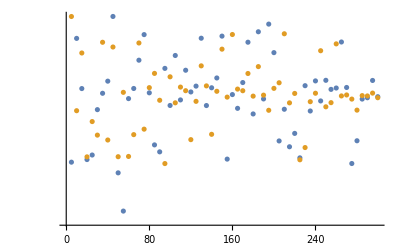

```mathematica
ListLogPlot[{Table[{v0sigmaB2mp[[i,1]],v0sigmaB2mp[[i,2]]/v0sigmaE2mp[[i,2]]},{i,1,Length[v0sigmaB2mp]}],Table[{v0sigmaB15[[i,1]],v0sigmaB15[[i,2]]/v0sigmaE15[[i,2]]},{i,1,Length[v0sigmaB15]}]},PlotRange->All]
```

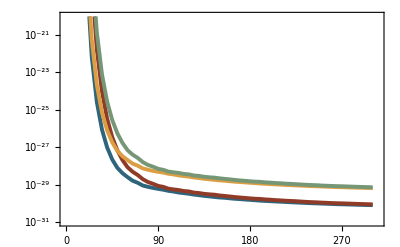

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/XQC_bounds_vPeak.pdf

```mathematica
vpeakSigma=ListLogPlot[{v0sigmaE2mp[[All,1;;2]],v0sigmaE15[[All,1;;2]],v0sigmaB2mp[[All,1;;2]],v0sigmaB15[[All,1;;2]]},Joined->True,PlotStyle->{{ColorData[17][9],Thickness[0.007]},{ColorData[17][2],Thickness[0.007]},{ColorData[17][4],Thickness[0.007]},{ColorData[17][6],Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{MaTeX["ES\\;m=2\\,m_p"],MaTeX["ES\\;m=1.5\\,GeV"],MaTeX["BS\\;m=2\\,m_p"],MaTeX["BS\\;m=1.5\\,GeV"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-31,-20}],None},{Table[30k,{k,0,10}],None}},PlotRange->{{0,305},{10^-31,10^-20}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["v_{peak}\\;(\\;km/s\\;)"],""}}]
Export[FigPath[PathNumber]<>"XQC_bounds_vPeak.pdf",vpeakSigma,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

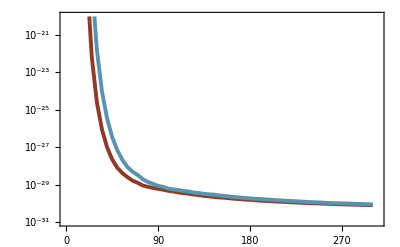

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/XQC_bounds_vPeak_ES.pdf

```mathematica
vpeakSigma3=ListLogPlot[{v0sigmaE2mp[[All,1;;2]],v0sigmaE15[[All,1;;2]]},Joined->True,PlotStyle->{{ColorData[17][2],Thickness[0.007]},{ColorData[17][8],Thickness[0.007]}},Frame->True,PlotLegends->Placed[LineLegend[{MaTeX["2\\,m_p"],MaTeX["1.5\\,GeV"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1},LegendLabel->MaTeX["m="]],{0.7,.7}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-31,-20,2}],None},{Table[30k,{k,0,10}],Table[30k,{k,0,10}]}},PlotRange->{{0,305},{10^-31,10^-20}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["v_{peak}\\;(\\;km/s\\;)"],""}}]
Export[FigPath[PathNumber]<>"XQC_bounds_vPeak_ES.pdf",vpeakSigma3,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
mp=0.938;
mT[A_]:=A*mp;
reduced[m1_,m2_]:=m1 m2/(m1+m2);
Al=27;
si[mH_]:=1.78*10^-24 *Al*mp*(reduced[mH,mp]/reduced[mH,Al*mp]/Al)^2;
siAl=Table[{mH,si[mH]},{mH,.3,100}];
```

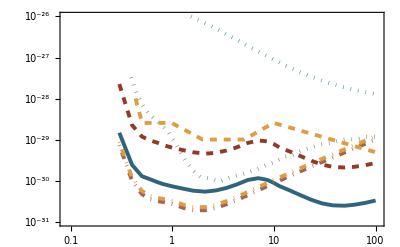

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/XQC_bound_chi2(v3).pdf

```mathematica
XQCG=ListLogLogPlot[{chi2earth[[All,1;;2]],sZF05,ZF05C[[All,1;;2]],Table[{ZF05C[[i,1]],9.0256ZF05C[[i,2]]/7.565},{i,Length[ZF05C]}],chi2body[[All,1;;2]],chi2E,siAl},Joined->True,PlotStyle->{{ColorData[17][9],Thickness[0.007]},{ColorData[17][6],Thickness[0.007],Dotted},{ColorData[17][3],Thickness[0.007],DotDashed},{ColorData[17][4],Thickness[0.007],DotDashed},{ColorData[17][2],Thickness[0.007],Dashed},{ColorData[17][4],Thickness[0.007],Dashed},{ColorData[17][8],Thickness[0.007],Dotted}},Frame->True,PlotLegends->LineLegend[{MaTeX["Earth-shielding"],MaTeX["ZF05\\;plot"],MaTeX["ZF05\\,(b=54)"],MaTeX["ZF05\\,(b=82)"],MaTeX["Body-shielding"],MaTeX["Erickcek\\,et\\,al.\\;plot"],MaTeX["given\\;\\lambda_{Al}=1\\,cm"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-31,-26}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-31,10^-26}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
Export[FigPath[PathNumber]<>"XQC_bound_chi2(v3).pdf",XQCG,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

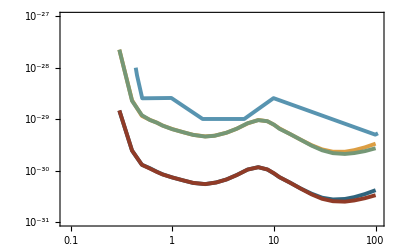

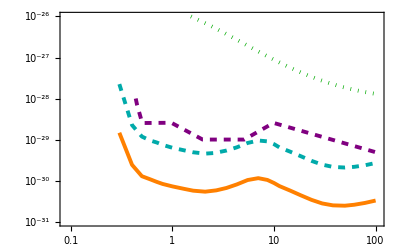

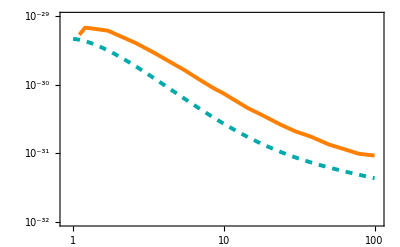

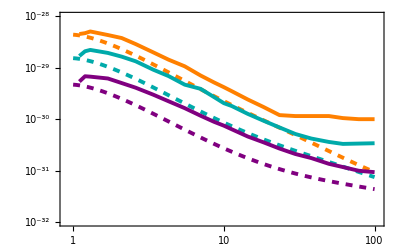

InterpolatingFunction::dmval: Input value {1.00009} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

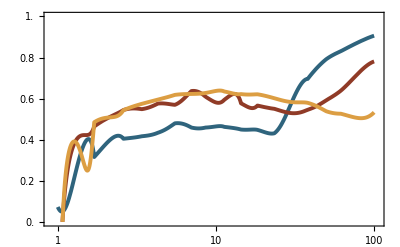

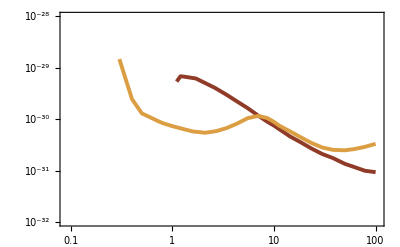

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/XQC_bound_chi2.pdf

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/XQC_bound_chi2(v2).pdf

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/DAMIC_bound.pdf

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/DAMIC_bound_differentdepths.pdf

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/DAMIC_UsSGED_difference.pdf

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/DAMIC&XQC_bounds.pdf

```mathematica
XQC=ListLogLogPlot[{chi2earthInt[[All,1;;2]],chi2earth[[All,1;;2]],chi2bodyInt[[All,1;;2]],chi2body[[All,1;;2]],chi2E},Joined->True,PlotStyle->{{ColorData[17][9],Thickness[0.007]},{ColorData[17][2],Thickness[0.007]},{ColorData[17][4],Thickness[0.007]},{ColorData[17][6],Thickness[0.007]},{ColorData[17][8],Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{MaTeX["Integral\\;method\\;ES"],MaTeX["Earth\\;shielded"],MaTeX["Integral\\;method\\;BS"],MaTeX["Body\\;shielded"],MaTeX["Erickcek\\;et\\,al.\\,plot"],MaTeX["given\\;\\lambda_{Al}=1\\,cm"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-31,-27}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-31,10^-27}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
XQCG=ListLogLogPlot[{chi2earth[[All,1;;2]],chi2body[[All,1;;2]],chi2E,siAl},Joined->True,PlotStyle->{{Orange,Thickness[0.007]},{Darker[Cyan],Thickness[0.007],Dashed},{Purple,Thickness[0.007],Dashed},{Darker[Green],Thickness[0.007],Dotted}},Frame->True,PlotLegends->LineLegend[{MaTeX["Earth-shielding"],MaTeX["Body-shielding"],MaTeX["Erickcek\\,et\\,al.\\;plot"],MaTeX["given\\,\\lambda_{Al}=1\\,cm"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-31,-26}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-31,10^-26}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
DAMIC100=ListLogLogPlot[{sDL100,sSGEDL100},Joined->True,PlotStyle->{{Orange,Thickness[0.007]},{Darker[Cyan],Dashed,Thickness[0.007]}},Frame->True,PlotLegends->Placed[LineLegend[{MaTeX["MF"],MaTeX["SGED\\;approx"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],{0.8,0.8}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-29}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},PlotRange->{{0.9,105},{10^-32,10^-29}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
DAMIC3depths=ListLogLogPlot[{sDL10,sSGEDL10,sDL30,sSGEDL30,sDL100,sSGEDL100},Joined->True,PlotStyle->{{Orange,Thickness[0.007]},{Orange,Thickness[0.007],Dashed},{Darker[Cyan],Thickness[0.007]},{Darker[Cyan],Thickness[0.007],Dashed},{Purple,Thickness[0.007]},{Purple,Dashed,Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{MaTeX["MF,\\;10\\;m"],MaTeX["SGED,\\;10\\;m"],MaTeX["MF,\\;30\\;m"],MaTeX["SGED,\\;30\\;m"],MaTeX["MF,\\;100\\;m"],MaTeX["SGED,\\;100\\;m"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},PlotRange->{{0.9,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
DAMICUsSGEDdifference=LogLinearPlot[{(sDL10I[x]-sSGEDL10I[x])/sDL10I[x],(sDL30I[x]-sSGEDL30I[x])/sDL30I[x],(sDL100I[x]-sSGEDL100I[x])/sDL100I[x]},{x,1,100},PlotStyle->{{ColorData[17][9],Thickness[0.007]},{ColorData[17][2],Thickness[0.007]},{ColorData[17][4],Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{MaTeX["10\\;m"],MaTeX["30\\;m"],MaTeX["100\\;m"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],FrameTicks->{{Table[0.1k,{k,0,10}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},PlotRange->{{0.9,105},{0,1}},FrameLabel->{{MaTeX["\\frac{\\sigma-\\sigma_{SGED}}{\\sigma}"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
XQCDAMIC=ListLogLogPlot[{sDL100,chi2earth[[All,1;;2]]},Joined->True,PlotStyle->{{ColorData[17][2],Thickness[0.007]},{ColorData[17][4],Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{MaTeX["DAMIC"],MaTeX["XQC\\;Earth\\;shielded"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
Export[FigPath[PathNumber]<>"XQC_bound_chi2.pdf",XQC,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
Export[FigPath[PathNumber]<>"XQC_bound_chi2(v2).pdf",XQCG,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
Export[FigPath[PathNumber]<>"DAMIC_bound.pdf",DAMIC100,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
Export[FigPath[PathNumber]<>"DAMIC_bound_differentdepths.pdf",DAMIC3depths,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
Export[FigPath[PathNumber]<>"DAMIC_UsSGED_difference.pdf",DAMICUsSGEDdifference,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
Export[FigPath[PathNumber]<>"DAMIC&XQC_bounds.pdf",XQCDAMIC,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
{sDL30,sSGEDL30}{sDL100,sSGEDL100}
```

```mathematica
DAMIC10=ListLogLogPlot[{sDL10,sSGEDL10},Joined->True,PlotStyle->{{Orange,Thickness[0.007]},{Orange,Thickness[0.007],Dashed}},Frame->True,PlotLegends->LineLegend[{MaTeX["MF,\\;10\\;m"],MaTeX["SGED,\\;10\\;m"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},PlotRange->{{0.9,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
DAMIC30=ListLogLogPlot[{sDL30,sSGEDL30},Joined->True,PlotStyle->{{Darker[Cyan],Thickness[0.007]},{Darker[Cyan],Thickness[0.007],Dashed}},Frame->True,PlotLegends->LineLegend[{MaTeX["MF,\\;30\\;m"],MaTeX["SGED,\\;30\\;m"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},PlotRange->{{0.9,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
DAMIC100p=ListLogLogPlot[{sDL100,sSGEDL100},Joined->True,PlotStyle->{{Purple,Thickness[0.007]},{Purple,Dashed,Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{MaTeX["MF,\\;100\\;m"],MaTeX["SGED,\\;100\\;m"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},PlotRange->{{0.9,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
DAMIC3depths=Show[DAMIC10,DAMIC30,DAMIC100p]
Export[FigPath[PathNumber]<>"DAMIC_3depths.pdf",DAMIC3depths,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

-Graphics-

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/DAMIC_3depths.pdf

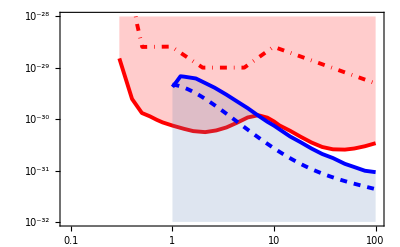

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/DAMIC&XQC_bounds_v1.pdf

```mathematica
Erickcek=ListLogLogPlot[chi2E,Joined->True,PlotStyle->{Thickness[0.007],Red,DotDashed},Frame->True,PlotLegends->LineLegend[{MaTeX["XQC\\;
Erickcek\\;etal"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendMarkerSize->{22,10}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
Starkman=ListLogLogPlot[sSGEDL100,Joined->True,PlotStyle->{Thickness[0.007],Blue,Dashed},Frame->True,PlotLegends->LineLegend[{MaTeX["DAMIC\\;SGED"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendMarkerSize->{22,10}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
DAMIC=ListLogLogPlot[{Table[{x,10^-33},{x,logspace[1,110,100]}],sDL100},Filling->{1->{2}},FillingStyle->{Opacity[0.2],LightBlue},Joined->True,PlotStyle->{{None},{Blue,Thickness[0.007]}},Frame->True,PlotStyle->Transparent,PlotLegends->LineLegend[{None,MaTeX["DAMIC\\;MF"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
XQC=ListLogLogPlot[{Table[{x,10^-27},{x,logspace[0.3,100,100]}],chi2earth[[All,1;;2]]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Red},Joined->True,PlotStyle->{{None},{Red,Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{None,MaTeX["XQC\\;MF"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
XQCDAMICv1=Show[Erickcek,XQC,DAMIC,Starkman]
Export[FigPath[PathNumber]<>"DAMIC&XQC_bounds_v1.pdf",XQCDAMICv1,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
Erickcek=ListLogLogPlot[chi2E,Joined->True,PlotStyle->{Thickness[0.007],Orange,DotDashed},Frame->True,FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
Starkman=ListLogLogPlot[sSGEDL100,Joined->True,PlotStyle->{Thickness[0.007],Darker[Cyan],Dashed},Frame->True,FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
DAMIC=ListLogLogPlot[{Table[{x,10^-33},{x,logspace[1,110,100]}],Join[{{0.95,10^-32},{0.97,4*10^-30}},sDL100]},Joined->True,Filling->{1->{2}},FillingStyle->{Opacity[0.1],Cyan},PlotStyle->{{None},{Darker[Cyan],Thickness[0.007]}},Frame->True,PlotLegends->Placed[LineLegend[{None,MaTeX["DAMIC"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],{1.8*10^-1,2.5*10^-1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
XQC=ListLogLogPlot[{Table[{x,10^-27},{x,logspace[0.3,100,100]}],Join[{{0.29,10^-28}},chi2earth[[All,1;;2]]]},Filling->{1->{2}},FillingStyle->{Opacity[0.5],Orange},Joined->True,PlotStyle->{{None},{Orange,Thickness[0.007]}},Frame->True,PlotLegends->Placed[LineLegend[{None,MaTeX["XQC"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"ReversedColumn",1}],{1.5*10^-1,4*10^-1}],FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-32,-28}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-32,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
textE=Graphics[Text[Rotate[MaTeX["
Erickcek\\;et\\,al."],-Pi/10],{Log[30],Log[2*10^-29]}]];
textS=Graphics[Text[Rotate[MaTeX["
SGED\\;approx"],-Pi/9],{Log[20],Log[6*10^-32]}]];
XQCDAMICv2=Show[XQC,textE,Erickcek,DAMIC,Starkman,textS]
Export[FigPath[PathNumber]<>"DAMIC&XQC_bounds_v2.pdf",XQCDAMICv2,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

-Graphics-

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/DAMIC&XQC_bounds_v2.pdf

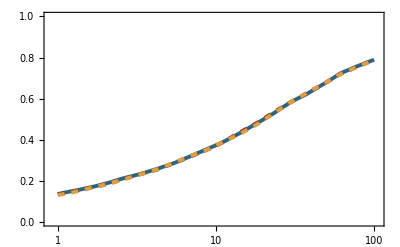

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/termalization_probability.pdf

```mathematica
termalization=ListLogLinearPlot[{term10[[All,1;;3;;2]],term30[[All,1;;3;;2]],term100[[All,1;;3;;2]]},Joined->True,PlotStyle->{{ColorData[17][9],Thickness[0.007]},{ColorData[17][2],Thickness[0.007],Dashed},{ColorData[17][4],Thickness[0.007],Dashed}},Frame->True,PlotRange->{{0.9,105},{0,1}},PlotLegends->Placed[LineLegend[{MaTeX["10\\;m"],MaTeX["30\\;m"],MaTeX["100\\;m"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],{.2,.7}],FrameLabel->{{MaTeX["Probability\\;of\\;termalization\\;in\\;Earth\\;potential"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
Export[FigPath[PathNumber]<>"termalization_probability.pdf",termalization,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
term10[[All,1;;3;;2]]
```

{{1.00000000000000022,0.135239999999999999},{1.10000000000000031,0.142490000000000006},{1.20000000000000018,0.148189999999999988},{1.30000000000000027,0.152879999999999988},{1.70000000000000018,0.172369999999999995},{2.10000000000000009,0.190689999999999998},{2.60000000000000009,0.212400000000000006},{3.40000000000000036,0.235110000000000013},{4.29999999999999982,0.259529999999999983},{5.5,0.287690000000000001},{7.,0.321840000000000015},{8.59999999999999965,0.351210000000000022},{10.0000000000000018,0.373219999999999996},{11.3000000000000025,0.391720000000000013},{14.4000000000000021,0.435180000000000011},{18.3000000000000007,0.481439999999999979},{23.4000000000000021,0.530669999999999975},{29.8000000000000007,0.583940000000000015},{38.,0.625099999999999989},{49.8000000000000043,0.679069999999999951},{61.6000000000000014,0.724110000000000031},{78.5,0.758240000000000025},{100.000000000000028,0.789420000000000011}}

```mathematica
XQCg=ListLogLogPlot[{chi2earthG220,chi2earthG30},Joined->True,PlotStyle->{{Thickness[0.007],Orange,DotDashed},{Thickness[0.007],Blue,Dotted}},Frame->True,FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-31,-27}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-31,10^-27}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];

XQC=ListLogLogPlot[{Table[{x,10^-25},{x,logspace[0.3,100,100]}],chi2earth[[All,1;;2]]},Filling->{1->{2}},FillingStyle->{Opacity[0.2],Red},Joined->True,PlotStyle->{{None},{Red,Thickness[0.007]}},Frame->True,FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-31,-27}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-31,10^-27}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
text30=Graphics[Text[Rotate[MaTeX["
v_0=30\\;km/s"],-Pi/5],{Log[15],Log[.5*10^-28]}]];
XQCDAMICg=Show[XQC,XQCg,text30]
Export[FigPath[PathNumber]<>"XQC_bounds_vG.pdf",XQCDAMICg,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

-Graphics-

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/XQC_bounds_vG.pdf

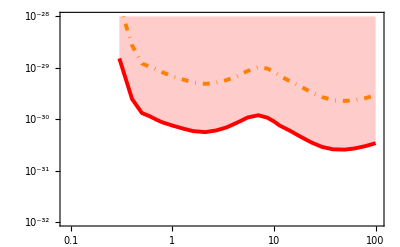

```mathematica
XQCb=ListLogLogPlot[{chi2body[[All,1;;2]]},Joined->True,PlotStyle->{{Thickness[0.007],Orange,DotDashed},{Thickness[0.007],Blue,Dotted}},Frame->True,FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-31,-27}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},PlotRange->{{0.09,105},{10^-31,10^-28}},FrameLabel->{{MaTeX["\\sigma_p\\;(\\;cm^2\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
XQCDAMICg=Show[XQC,XQCb]
```

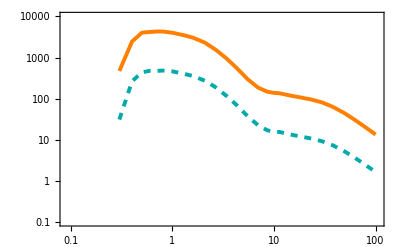

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Latex/Figures/XQC_lambdas.pdf

```mathematica
XQClambda=ListLogLogPlot[{chi2earth[[All,1;;16;;15]],chi2body[[All,1;;16;;15]]},Joined->True,PlotStyle->{{Orange,Thickness[0.007]},{Darker[Cyan],Thickness[0.007],Dashed}},Frame->True,PlotRange->{{0.09,105},{10^-1,10^4}},FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-1,4}],None},{Table[{10^k,Superscript[10,k]},{k,-1,3}],None}},FrameLabel->{{MaTeX["\\lambda_{eff}\\;(\\;cm\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
Export[FigPath[PathNumber]<>"XQC_lambdas.pdf",XQClambda,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

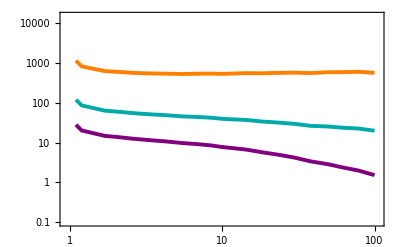

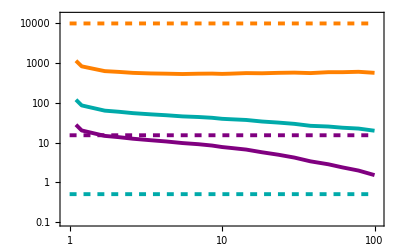

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/DAMIC_lambdas.pdf

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/DAMIC_lambdas(v2).pdf

```mathematica
DAMIClambda=ListLogLogPlot[{leff,lCu,lPb},Joined->True,PlotStyle->{{Orange,Thickness[0.007]},{Darker[Cyan],Thickness[0.007]},{Purple,Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{MaTeX["Earth's\\,crust"],MaTeX["Cu"],MaTeX["Pb"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],PlotRange->{{0.95,105},{10^-1,1.5 10^4}},FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-1,4}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},FrameLabel->{{MaTeX["\\lambda\\;(\\;cm\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}];
DAMIClambda2=ListLogLogPlot[{leff,lCu,lPb},Joined->True,PlotStyle->{{Orange,Thickness[0.007]},{Darker[Cyan],Thickness[0.007]},{Purple,Thickness[0.007]}},Frame->True,PlotLegends->LineLegend[{MaTeX["Earth's\\,crust\\,(10^4\\,cm)"],MaTeX["Cu\\,(0.5\\,cm)"],MaTeX["Pb\\,(15\\,cm)"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],PlotRange->{{0.95,105},{10^-1,1.5 10^4}},FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-1,4}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},FrameLabel->{{MaTeX["\\lambda\\;(\\;cm\\;)"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
d=ListLogLogPlot[{Table[{mH,10000},{mH,1,100}],Table[{mH,0.5},{mH,1,100}],Table[{mH,15.24},{mH,1,100}]},Joined->True,PlotStyle->{{Orange,Thickness[0.007],Dashed},{Darker[Cyan],Thickness[0.007],Dashed},{Purple,Thickness[0.007],Dashed}}];
save=Show[DAMIClambda,d]
Export[FigPath[PathNumber]<>"DAMIC_lambdas.pdf",save,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
Export[FigPath[PathNumber]<>"DAMIC_lambdas(v2).pdf",DAMIClambda2,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

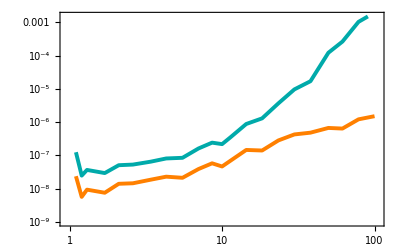

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/DAMIC_att.pdf

```mathematica
att=ListLogLogPlot[{attPb,attSi},Joined->True,PlotStyle->{{Darker[Cyan],Thickness[0.007]},{Orange,Thickness[0.007]}},Frame->True,PlotLegends->Placed[LineLegend[{MaTeX["Earth's\\,crust"],MaTeX["Earth's\\,crust+lead\\,shield"]},LabelStyle->{FontFamily-> "CMU Serif",11},LegendLayout->{"Column",1}],{0.32,0.8}],PlotRange->{{0.95,105},{10^-9,1.5 10^-3}},FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-9,-3}],None},{Table[{10^k,Superscript[10,k]},{k,0,3}],None}},FrameLabel->{{MaTeX["attenuation\\;factor"],""},{MaTeX["m\\;(\\;GeV\\;)"],""}}]
Export[FigPath[PathNumber]<>"DAMIC_att.pdf",att,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```